# Introducción a Mathematica

## Ejemplo básico:

Un campo direccional simple  con la condición inicial

### a) StreamPlot / VectorPlot

Para visualizar el campo direccional en el plano  o (en general) , solemos usar  o . Sin embargo, para 1D solemos graficar la pendiente en un solo eje. Un ejemplo en 2D sería forzar una ecuación como

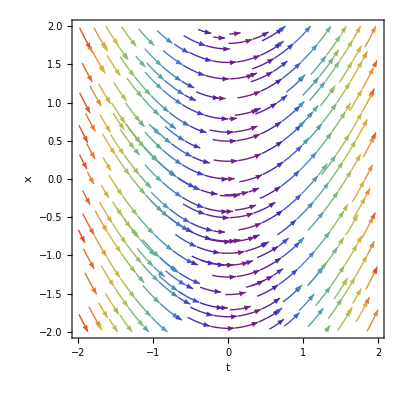

```mathematica
(* Versión 1D: dx/dt = x, "falsa" visualización en 2D para practicar *)
StreamPlot[{1, x}, {x, -2, 2}, {t, -2, 2}, StreamColorFunction -> "Rainbow", AxesLabel -> {"t", "x"}]
```

Este truco pone 1 para la componente en el eje horizontal (que sería t) y x como la componente vertical (d/dt), simulando las pendientes.

### b) Solución analítica con DSolve

```mathematica
sol = DSolve[{x'[t] == x[t], x[0] == x0}, x[t], t]
```

{{x[t]→ⅇ^t x0}}

### c) Graficar la solución con Plot

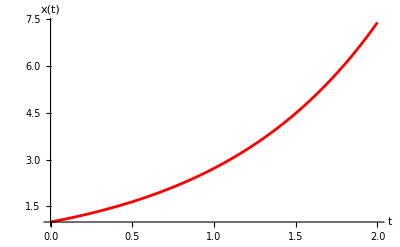

```mathematica
Plot[Evaluate[x[t] /. sol /. x0 -> 1], {t, 0, 2}, 
 AxesLabel -> {"t", "x(t)"}, PlotStyle -> Red]
```

Tenemos que fijar =1 para obtener una solución.

#### d) Solución numérica con NDSolve

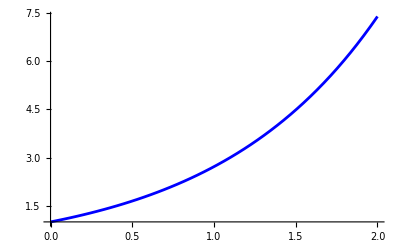

```mathematica
solNum = NDSolve[{x'[t] == x[t], x[0] == 1}, x, {t, 0, 2}];
Plot[Evaluate[x[t] /. solNum], {t, 0, 2}, PlotStyle -> Blue]
```

En problemas más complicados (no solucionables con ),  es la opción.

## Campos direccionales en 2 variables

Para un sistema 	 podemos usar VectorPlot o StreamPlot.

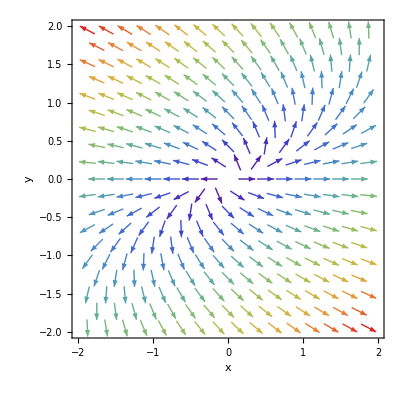

```mathematica
f[x_, y_] := x - y;
g[x_, y_] := y;

VectorPlot[{f[x,y], g[x,y]}, {x, -2, 2}, {y, -2, 2},
 VectorColorFunction -> "Rainbow",
 AxesLabel -> {"x", "y"}]
```

Esto muestra las flechas del campo  en la región

## Modelo presa-depredador simple (Lotka-Volterra)

donde:
𝑥 = población de presas,
𝑦 = población de depredadores,
𝑎,𝑏,𝑐,𝑑 son constantes positivas.

#### a) VectorPlot del campo

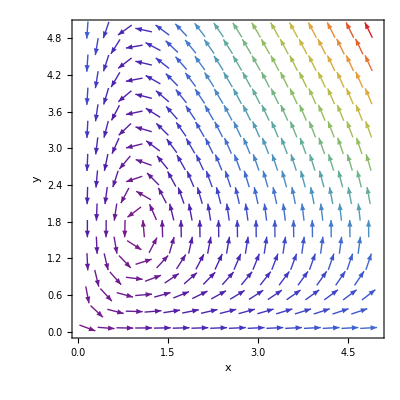

```mathematica
a = 0.5; b = 0.3; c = 0.5; d = 0.5;
f[x_, y_] := a*x - b*x*y;
g[x_, y_] := -c*y + d*x*y;

VectorPlot[{f[x, y], g[x, y]}, {x, 0, 5}, {y, 0, 5},
 VectorColorFunction -> "Rainbow",
 PlotRange -> All,
 AxesLabel -> {"x", "y"}]
```

#### b) Solución numérica con NDSolve

Fijamos condiciones iniciales, por ejemplo:   y

```mathematica
solLV = NDSolve[
  {x'[t] == f[x[t], y[t]],
   y'[t] == g[x[t], y[t]],
   x[0] == 1.5, y[0] == 1.0},
  {x, y}, {t, 0, 20}
];
```

#### c) Graficar soluciones

#### En el tiempo:

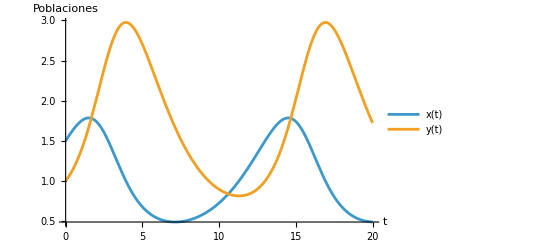

```mathematica
Plot[
  Evaluate[{x[t], y[t]} /. solLV], {t, 0, 20}, 
  PlotLegends -> {"x(t)", "y(t)"}, 
  AxesLabel -> {"t", "Poblaciones"}
]
```

#### Plano fase (𝑥,𝑦)

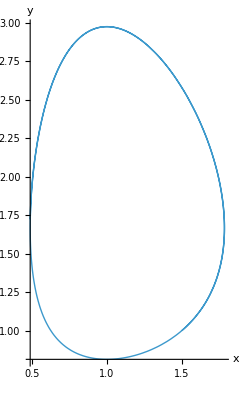

```mathematica
ParametricPlot[
  Evaluate[{x[t], y[t]} /. solLV], {t, 0, 20},
  PlotRange -> All,
  PlotStyle -> Thick,
  AxesLabel -> {"x", "y"}
]
```